```mathematica
KM ={{k, -k}, {-k, 2*k}};
MM = {{m, 0 }, {0, m}};
MI = Inverse[MM]//Simplify;
MInvK = MI.KM//Simplify;
MInvK//MatrixForm
Eigensystem[MInvK]
```

(k/m | -k/m
-k/m | (2 k)/m)

{{((3+√5) k)/(2 m),((3-√5) k)/(2 m)},{{1/2 (1-√5),1},{1/2 (1+√5),1}}}

```mathematica
eq1 = m*q1''[t] == -k*q1[t] + k*q2[t]
eq2 = m*q2''[t] == k* q1[t] -2*k*q2[t]
```

m q1''[t]==-k q1[t]+k q2[t]

m q2''[t]==k q1[t]-2 k q2[t]

First Mode

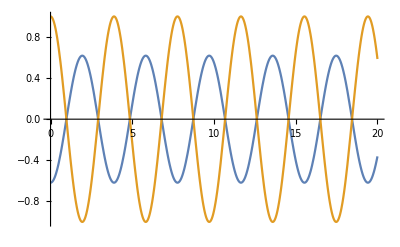

-Graphics-

Second Mode

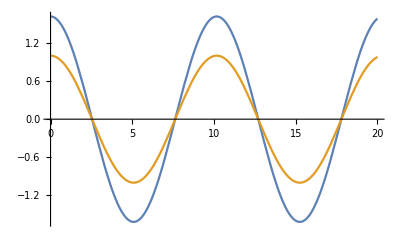

-Graphics-

```mathematica
m = 1;
k = 1;
IC1 = {q1[0]==(1 - Sqrt[5])/2, q2[0] == 1, q1'[0] == 0, q2'[0]==0};
IC2 = {q1[0]==(1 + Sqrt[5])/2, q2[0] == 1, q1'[0] == 0, q2'[0]==0};
IC3 = {q1[0]==1, q2[0] == -1/2, q1'[0] == 0.34, q2'[0]==Pi};
sol1 = DSolve[{eq1, eq2, IC1}, {q1[t], q2[t]}, t];
sol2 = DSolve[{eq1, eq2, IC2}, {q1[t], q2[t]}, t];
sol3 = DSolve[{eq1, eq2, IC3}, {q1[t], q2[t]}, t];
Print["First Mode"]
Plot[{q1[t]/.sol1, q2[t]/.sol1}, {t, 0, 20}]
Plot[{(1 - Sqrt[5])*Cos[Sqrt[(3+Sqrt[5])/2]*t]/2, 1*Cos[Sqrt[(3+Sqrt[5])/2]*t]}, {t, 0, 20}]
Print["Second Mode"]
Plot[{q1[t]/.sol2, q2[t]/.sol2}, {t, 0, 20}]
Plot[{(1 + Sqrt[5])*Cos[Sqrt[(3-Sqrt[5])/2]*t]/2, 1*Cos[Sqrt[(3-Sqrt[5])/2]*t]}, {t, 0, 20}]
(*
Plot[{q1[t]/.sol3, q2[t]/.sol3}, {t, 0, 20}];)*
```

```mathematica
KM ={{k, 0}, {0, k}};
MM = {{3*m, m }, {m, m}};
MI = Inverse[MM]//Simplify;
MInvK = MI.KM//Simplify;
MInvK//MatrixForm
Eigensystem[MInvK]
expr = (k -3*m*ω^2)*(k - m*ω^2) - (ω^2m)^2 == 0;
Solve[expr, ω]
```

(k/(2 m) | -k/(2 m)
-k/(2 m) | (3 k)/(2 m))

{{((2+√2) k)/(2 m),((2-√2) k)/(2 m)},{{1-√2,1},{1+√2,1}}}

{{ω→-√(k/m+k/(√2 m))},{ω→√(k/m+k/(√2 m))},{ω→-(√((2 k)/m-(√2 k)/m))/(√2)},{ω→(√((2 k)/m-(√2 k)/m))/(√2)}}

# Homework 33

No Mathematica problems today!

## Written Problems

-Graphics-